# p-wave Depletion

## 全局设定

```mathematica
Clear["Global`*"]
```

```mathematica
$Assumptions={g1∈Reals &&g2∈Reals && g12∈Reals  && g1>0 && g2>0 && g12<0 && n>0&&A>0&& g3>0};
```

## 写出κM的表达式

```mathematica
M={{A-u+2g n+A g3 n+g12 n,g n,n(g12-g3 A),n g12},{g n,A-u+2g n+g12 n+A g3 n,n g12,n(g12-g3 A)},{n(g12-g3 A),n g12,A-u+2g n+g12 n+A g3 n,g n},{n g12,n(g12-g3 A),g n,A-u+2g n+g12 n+A g3 n}}
```

{{A+2 g n+g12 n+A g3 n-u,g n,(g12-A g3) n,g12 n},{g n,A+2 g n+g12 n+A g3 n-u,g12 n,(g12-A g3) n},{(g12-A g3) n,g12 n,A+2 g n+g12 n+A g3 n-u,g n},{g12 n,(g12-A g3) n,g n,A+2 g n+g12 n+A g3 n-u}}

```mathematica
MatrixForm[M]
```

(A+2 g n+g12 n+A g3 n-u | g n | (g12-A g3) n | g12 n
g n | A+2 g n+g12 n+A g3 n-u | g12 n | (g12-A g3) n
(g12-A g3) n | g12 n | A+2 g n+g12 n+A g3 n-u | g n
g12 n | (g12-A g3) n | g n | A+2 g n+g12 n+A g3 n-u)

```mathematica
κ={{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}
```

{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
DiagonalMatrix[{1,-1,1,-1}]
```

{{1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,-1}}

```mathematica
MatrixForm[κ]
```

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | -1)

```mathematica
H1=Dot[κ,M]
```

{{A+2 g n+g12 n+A g3 n-u,g n,(g12-A g3) n,g12 n},{-g n,-A-2 g n-g12 n-A g3 n+u,-g12 n,-((g12-A g3) n)},{(g12-A g3) n,g12 n,A+2 g n+g12 n+A g3 n-u,g n},{-g12 n,-((g12-A g3) n),-g n,-A-2 g n-g12 n-A g3 n+u}}

```mathematica
MatrixForm[H1]
```

(A+2 g n+g12 n+A g3 n-u | g n | (g12-A g3) n | g12 n
-g n | -A-2 g n-g12 n-A g3 n+u | -g12 n | -((g12-A g3) n)
(g12-A g3) n | g12 n | A+2 g n+g12 n+A g3 n-u | g n
-g12 n | -((g12-A g3) n) | -g n | -A-2 g n-g12 n-A g3 n+u)

## 求 (Tr(κM))^2

```mathematica
H2=Dot[H1,H1]
```

{{-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+2 g n+g12 n+A g3 n-u)^2,g n (A+2 g n+g12 n+A g3 n-u)+g n (-A-2 g n-g12 n-A g3 n+u),-2 g g12 n^2+2 (g12-A g3) n (A+2 g n+g12 n+A g3 n-u),g12 n (A+2 g n+g12 n+A g3 n-u)+g12 n (-A-2 g n-g12 n-A g3 n+u)},{-g n (A+2 g n+g12 n+A g3 n-u)-g n (-A-2 g n-g12 n-A g3 n+u),-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(-A-2 g n-g12 n-A g3 n+u)^2,-g12 n (A+2 g n+g12 n+A g3 n-u)-g12 n (-A-2 g n-g12 n-A g3 n+u),-2 g g12 n^2-2 (g12-A g3) n (-A-2 g n-g12 n-A g3 n+u)},{-2 g g12 n^2+2 (g12-A g3) n (A+2 g n+g12 n+A g3 n-u),g12 n (A+2 g n+g12 n+A g3 n-u)+g12 n (-A-2 g n-g12 n-A g3 n+u),-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+2 g n+g12 n+A g3 n-u)^2,g n (A+2 g n+g12 n+A g3 n-u)+g n (-A-2 g n-g12 n-A g3 n+u)},{-g12 n (A+2 g n+g12 n+A g3 n-u)-g12 n (-A-2 g n-g12 n-A g3 n+u),-2 g g12 n^2-2 (g12-A g3) n (-A-2 g n-g12 n-A g3 n+u),-g n (A+2 g n+g12 n+A g3 n-u)-g n (-A-2 g n-g12 n-A g3 n+u),-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(-A-2 g n-g12 n-A g3 n+u)^2}}

```mathematica
a1=FullSimplify[Tr[H2]/4]
```

-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+2 g n+g12 n+A g3 n-u)^2

## 求Det(κM)

```mathematica
a2=FullSimplify[Det[H1]]
```

(A+(g+g12) n-u) (A+3 (g+g12) n-u) (A+3 g n-g12 n+2 A g3 n-u) (A+(g+g12) n+2 A g3 n-u)

## 激发谱以及求激发的粒子数

```mathematica
Clear["Global`*"]
```

```mathematica
spec1=√(a1+√((a1)^2-a2))
```

√(-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+√((-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+2 g n+g12 n+A g3 n-u)^2)^2-(A+(g+g12) n-u) (A+3 (g+g12) n-u) (A+3 g n-g12 n+2 A g3 n-u) (A+(g+g12) n+2 A g3 n-u))+(A+2 g n+g12 n+A g3 n-u)^2)

```mathematica
spec2=√(a1-√((a1)^2-a2))
```

√(-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2-√((-g^2 n^2-g12^2 n^2+(g12-A g3)^2 n^2+(A+2 g n+g12 n+A g3 n-u)^2)^2-(A+(g+g12) n-u) (A+3 (g+g12) n-u) (A+3 g n-g12 n+2 A g3 n-u) (A+(g+g12) n+2 A g3 n-u))+(A+2 g n+g12 n+A g3 n-u)^2)

```mathematica
n1=D[spec1,u];
```

```mathematica
n2=D[spec2,u];
```

## 将u1，u2带回去

```mathematica
u=g n+g12 n;
```

```mathematica
Simplify[spec1]
```

√(A (A+2 g n+2 A g3 n+2 g g3 n^2-2 g12 g3 n^2+2 A g3^2 n^2+2 n √((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))

## 化简n1

```mathematica
FullSimplify[n1]
```

(-g12^2 n (1+g3 n)+g12 g3 n (g n+2 A (1+g3 n))-(A+g n+A g3 n) (A g3^2 n+√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))/(√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2) √(A (A+2 A g3 n (1+g3 n)+2 n (g+(g-g12) g3 n+√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))))

```mathematica
-g12^2 n^2(1+g3 n)+g12 g3 n^2 (g n+2 A (1+g3 n))-(A+g n+A g3 n) (A g3^2 n^2+√((g12 n+g12 g3 n^2-g3 n(A+g n+A g3 n))^2)))/(√((g12 n+g12 g3 n^2-g3 n(A+g n+A g3 n))^2) √(A (A+2 A g3 n (1+g3 n)+2 n (g+(g-g12) g3 n+√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))))
```

```mathematica
FullSimplify[n2]
```

(g12^2 n (1+g3 n)-g12 g3 n (g n+2 A (1+g3 n))+(A+g n+A g3 n) (A g3^2 n-√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))/(√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2) √(A (A+2 A g3 n (1+g3 n)+2 n (g+(g-g12) g3 n-√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))))

```mathematica
Expand[-g12^2 n (1+g3 n)+g12 g3 n (g n+2 A (1+g3 n))-(A+g n+A g3 n) A g3^2 n]
```

-g12^2 n+2 A g12 g3 n-A^2 g3^2 n+g g12 g3 n^2-g12^2 g3 n^2-A g g3^2 n^2+2 A g12 g3^2 n^2-A^2 g3^3 n^2

```mathematica
FullSimplify[n2]
```

(g12^2 n (1+g3 n)-g12 g3 n (g n+2 A (1+g3 n))+(A+g n+A g3 n) (A g3^2 n-√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))/(√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2) √(A (A+2 A g3 n (1+g3 n)+2 n (g+(g-g12) g3 n-√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))))

## 分子

```mathematica
FullSimplify[-B^3 y^2(1+y)+B^2 y(-y+2x(1+y))-B(x+x y-y(B+1+B y))+B(x y-x^2(1+y)-(1+y)B(x+x y-y(B+1+B y)))]
```

B (1+B+x) (-x (1+y)+y (1+B+B y))

```mathematica
Expand[-B^3 y^2(1+y)+B^2 y(-y+2x(1+y))-B(x+x y-y(B+1+B y))+B(x y-x^2(1+y)-(1+y)B(x+x y-y(B+1+B y)))]
```

-B x-B^2 x-B x^2+B y+2 B^2 y+B^3 y-B x^2 y+B^2 y^2+B^3 y^2+B^2 x y^2

## 分母

```mathematica
FullSimplify[√(B (B+2 (1+B y) +2 y (1-x+B y) )+2 B (x+x y-y (B+1+B y)))]
```

-B √(B (2+B+2 x)) (-x (1+y)+y (1+B+B y))

```mathematica
FullSimplify[B (B+2 (1+B y) +2 y (1-x+B y) )+2 B (x+x y-y (B+1+B y))]
```

B (2+B+2 x)

## 化简n2

```mathematica
FullSimplify[n1]
```

(-g12^2 n (1+g3 n)+g12 g3 n (g n+2 A (1+g3 n))-(A+g n+A g3 n) (A g3^2 n+√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))/(√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2) √(A (A+2 A g3 n (1+g3 n)+2 n (g+(g-g12) g3 n+√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))))

```mathematica
FullSimplify[n2]
```

(g12^2 n (1+g3 n)-g12 g3 n (g n+2 A (1+g3 n))+(A+g n+A g3 n) (A g3^2 n-√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))/(√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2) √(A (A+2 A g3 n (1+g3 n)+2 n (g+(g-g12) g3 n-√((g12+g12 g3 n-g3 (A+g n+A g3 n))^2)))))

```mathematica
FullSimplify[B^3 y^2 (1+y)+B^2 y (y-2  (x+x y))-B  (x+x y-y(B+1+B y))+B (-x y+x^2 (1+y)-(1+y)B  (x+x y-y(1+B+B y)))]
```

B (1+B-x+2 B y) (-x (1+y)+y (1+B+B y))

```mathematica
FullSimplify[√(B (B+2 (1+B y) +2 y(1-x+B y))-2 B (x+x y-y (A+g n+A g3 n))^2)]
```

B (1+2 y) (2+B-2 x+2 B y)

```mathematica
B(x+x y-y(B+1+B y))
```

```mathematica
FullSimplify[B^3 y^2(1+y)+B^2 y(y-2x(1+y))-B(x+x y-y(B+1+B y))+B(-x y+x^2(1+y)-(1+y)B(x+x y-y(B+1+B y)))]
```

B (1+B-x+2 B y) (-x (1+y)+y (1+B+B y))

## 求发散

```mathematica
$Assumptions={ z>0&&y>0};
```

```mathematica
Series[(-C1^3 y^2(1+z)+C1 y z(C1^2+2C1(1+z))-C1(1+C1+z)(z^2+√((C1(y+y z)-z(1+C1+z))^2)))/(√((C1(y+y z)-z(1+C1+z))^2)√(1+2z(1+z)+2C1(1+z(1-y))+2 √((C1(y+y z)-z(1+C1+z))^2))),{C1,0,2}]
```

-((1+z) (z^2+√(z^2 (1+z)^2)) C1)/(√(z^2 (1+z)^2) √(1+2 z+2 z^2+2 √(z^2 (1+z)^2)))+O[C1]^3

```mathematica
Series[(C1^3 y^2(1+z)-C1 y z(C1^2+2C1(1+z))+C1(1+C1+z)(z^2-√((C1(y+y z)-z(1+C1+z))^2)))/(√((C1(y+y z)-z(1+C1+z))^2)√(1+2z(1+z)+2C1(1+z(1-y))-2 √((C1(y+y z)-z(1+C1+z))^2))),{C1,0,2}]
```

((1+z) (z^2-√(z^2 (1+z)^2)) C1)/(√(z^2 (1+z)^2) √(1+2 z+2 z^2-2 √(z^2 (1+z)^2)))+O[C1]^3

```mathematica
FullSimplify[%252+%255]
```

-2 C1+O[C1]^3

```mathematica
FullSimplify[(y^2(1+z)-y z(1+2B(1+z))+(B+1+B z)(B z^2-√((y+y z-z(B+1+B z))^2)))/(√((y+y z-z(B+1+B z))^2)√(B(B+2B z(1+z)+2(1+z(1-y))-2 √((y+y z-z(B+1+B z))^2))))+(-y^2(1+z)+y z(1+2B(1+z))-(B+1+B z)(B z^2+√((y+y z-z(B+1+B z))^2)))/(√((y+y z-z(B+1+B z))^2)√(B(B+2B z(1+z)+2(1+z(1-y))+2 √((y+y z-z(B+1+B z))^2))))]
```

$Aborted

```mathematica
FullSimplify[B+2B z(1+z)+2(1+z(1-y))+2(y+y z-z(B+1+B z))]
```

2+B+2 y

```mathematica
FullSimplify[B z^2+(y+y z-z(B+1+B z))]
```

-((1+B) z)+y (1+z)

```mathematica
FullSimplify[(y^2(1+z)-y z(1+2B(1+z))+(B+1+B z)(-y (1+z)+z (1+B+2 B z)))/((y+y z-z(B+1+B z))√(B(1+2 z) (2+B-2 y+2 B z)))+(-y^2(1+z)+y z(1+2B(1+z))-(B+1+B z)(-((1+B) z)+y (1+z)))/((y+y z-z(B+1+B z))√(B(2+B+2 y)))]
```

1/2 (-B/(√(B (2+B+2 y)))-B/(√((B (2+B-2 y+2 B z))/(1+2 z)))-(√(B (2+B+2 y))+√((B (2+B-2 y+2 B z))/(1+2 z)))/B)

```mathematica
Integrate[k^2(1/2 (-(k^2/2)/(√(k^2/2 (2+k^2/2+2 y)))-(k^2/2)/(√((k^2/2(2+k^2/2-2 y+2 k^2/2 z))/(1+2 z)))-(√(k^2/2(2+k^2/2+2 y))+√((k^2/2 (2+k^2/2-2 y+2 k^2/2 z))/(1+2 z)))/(k^2/2))+2),{k,0,∞}]
```

ConditionalExpression[-4/3 (√(1+y)+√((1-y)/(1+2 z)^3)+y (√(1+y)-√((1-y)/(1+2 z)^3))), y<1]

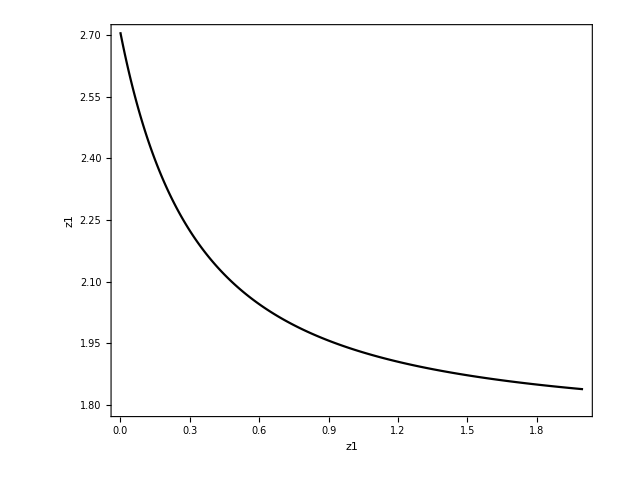

```mathematica
g[y_,z_]:=4/3 (√(1+y)+√((1-y)/(1+2 z)^3)+y (√(1+y)-√((1-y)/(1+2 z)^3)))
data2=Table[{z,g[0.2,z]},{z,0,2,0.001}];

(*生成表格数据*)
g2f=ListLinePlot[data2,PlotStyle->{Black},PlotRange->All,Ticks->{{0,2,4},{0,2,4,6,8}},AspectRatio->0.8,LabelStyle->Directive[15],Frame->{{True,True},{True,True}},AxesLabel->{"z1","z1"},AxesLabel->{"int1","n1+n2"}]

(*绘制图像*)
4/3 (-√(1-y)-√(1+y)+y (√(1-y)-√(1+y)))
```

```mathematica
Export["QD.eps",g2f]
```

QD.eps